```mathematica
Quit[];
```

```mathematica
(*parameter values for example in section 3.1 - Simulations in a theoretical context*)
tu=0.1;
tv=0.2;
bet=10;
ac=-19;
bc=10;
cc=10;
dc=-19;
```

```mathematica
(*function defining the Wilson-Cowan system*)
f[z_]:=1/(1+Exp[-bet*z]);
F[u_,ud_]:={
-u[[1]]+f[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium state*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{0.0478985,0.0511112}

```mathematica
(*characteristic parameter values*)
alpha=ac*f'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f'[tu+ac*eq[[1]]+bc*eq[[2]]]*f'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-17.8796

57.7268

```mathematica
(*verify the position of the point (alpha,beeta) with respect to the parabola alpha^2=4 beta -> the point is BELOW the parabola*)
beta-alpha^2/4
```

-22.1932

```mathematica
(*Dirac kernel - Laplace transform and related functions defined in paper*)
H[z_]:=Exp[-z];
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2*Re[Q[t,I*w]];
be[t_,w_]:=Abs[Q[t,I*w]]^2;
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=1; (*given explicitely for ease of computation*)
theta[w_]:=w; (*given explicitely for ease of computation*)
w1[t_]:=w/.FindRoot[Im[Q[t,I*w]]==0,{w,Pi/2,Pi}];
mu[w_]:=1/(rho[w]*Cos[theta[w]]);
```

```mathematica
(*Use Theorem 2.8 for the Dirac kernel, to detect critical value of time delay and frequency - along the line (l_tau) - because the point (alpha,beta) is BELOW the parabola *)
(*find possible values of mu_tau*)
mutau=x/.Solve[{beta==x*(alpha-x),x<-1},x];
(*find possible value of frequency w1 in the interval (Pi/2,Pi) according to Lemma 2.4 *)
wtau=Min[Table[w/.NSolve[{mu[w]==mutau[[k]],Pi/2<w<Pi},w][[1]],{k,1,Length[mutau]}]]
```

1.64412

```mathematica
(*find critical value of tau based on the formula of w_tau from Theorem 2.8 *)
Tau=tau/.Solve[wtau*Cos[theta[wtau]]+tau*Sin[theta[wtau[[]]]]==0,tau][[1]]
```

0.120766

```mathematica
(*predicted frequency of oscillations at Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=wtau/(Tau*2*Pi)
```

2.16675

```mathematica
(*stability region for Dirac kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared*)
pd[t_]:=
Show[RegionPlot[y>1/Co[t,w1[t]]*(x-1/Co[t,w1[t]])&&y>x-1&&x<2(Cos[t*Sqrt[y-1]]-Sqrt[y-1]*Sin[t*Sqrt[y-1]]),{x,2*mu[w1[t]],2},{y,mu[w1[t]],0.96*mu[w1[t]]^2},PlotPoints->100],
Plot[x-1,{x,1+1/Co[t,w1[t]],2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"Dirac, τ=",t}],Bold,20],Background->LightYellow,RoundingRadius->4],{1+mu[wtau],0.85*mu[wtau]^2}],
PlotRange->{{2*mu[wtau],2},{mu[wtau],0.96*mu[wtau]^2}}]
```

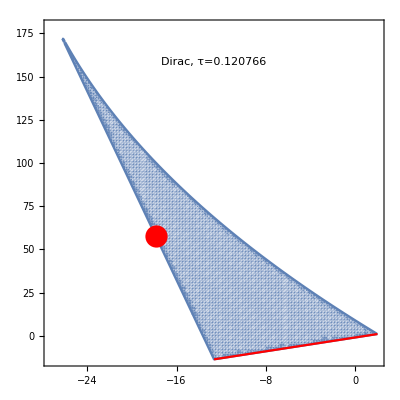

```mathematica
pd[Tau]
```

```mathematica
(*system with DIRAC kernel*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[2]],
 u[t /; t≤ 0]==eq[[1]]*1.1,
v[t /; t≤ 0]==eq[[2]]*1.1};
```

```mathematica
(*frequency at Hopf bifurcation computed based on the numerically evaluated solution - agrees with theoretically calculated value*)
Tmax=200;
pts=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{u[t-Tau],v[t-Tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-Tau],v[t-Tau]}][[2]],
 u[t /; t≤ 0]==eq[[1]]*1.1,
v[t /; t≤ 0]==eq[[2]]*1.1,WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,Tmax/2,Tmax}]][[2,1]];
frequency=1/Mean[Differences[pts,1,2]]
```

2.16753

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=20;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v},{t,Tmax}]],{t,0,Tmax-trans},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"u(t), v(t)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

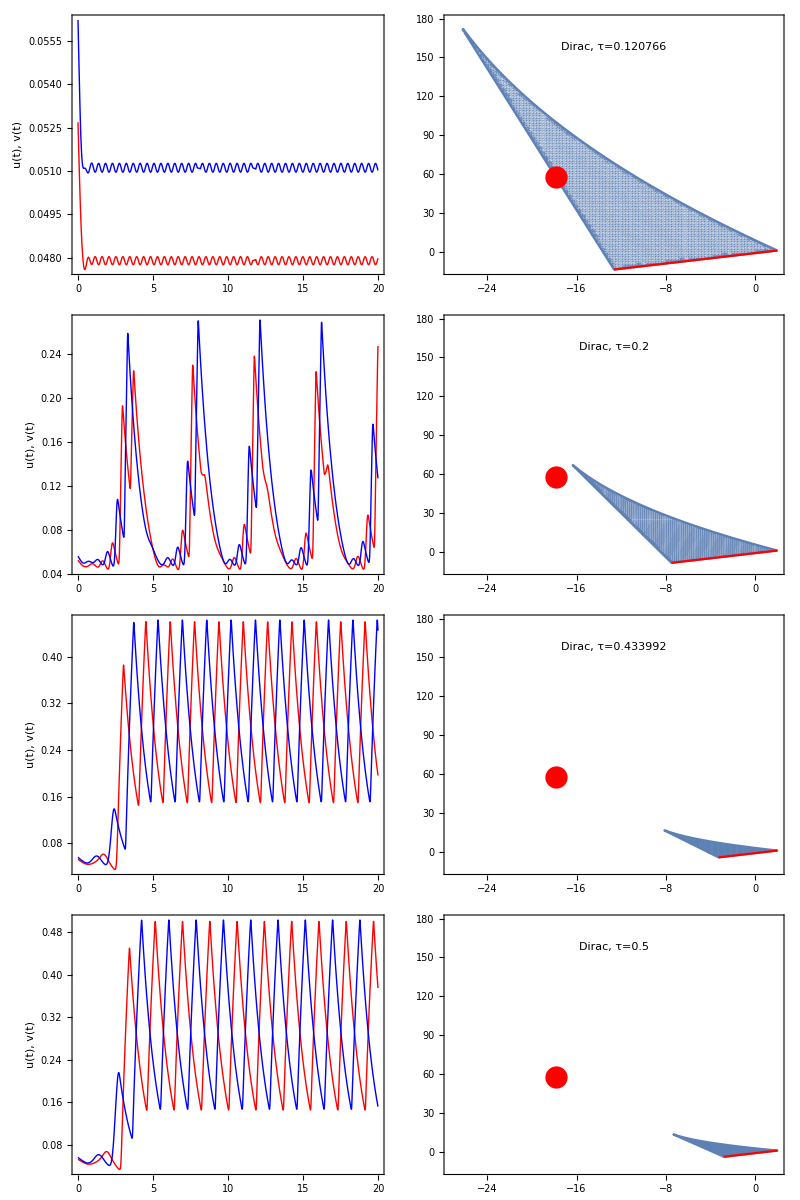

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[Tau],pd[Tau]},{p1[0.2],pd[0.2]},{p1[0.433992],pd[0.433992]},{p1[0.5],pd[0.5]}}]
```

```mathematica
Tmax=100;
trans=Tmax/2;
p2[tau_]:=ParametricPlot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v},{t,Tmax}]],{t,0,Tmax-trans},Axes->False,Frame->True,AspectRatio->1,PlotRange->All,PlotLabel->Row[Style[#,16] & /@{"τ=",tau}], LabelStyle->Directive[Bold,Black, Larger],(*ColorFunction->{Red, Blue}*)(* ColorFunction->Function[{t},Hue[0.5Sin[0.3 t]- 0.5*t]]*) ImageSize->{Automatic,300},FrameStyle->Directive[FontSize->16]]
```

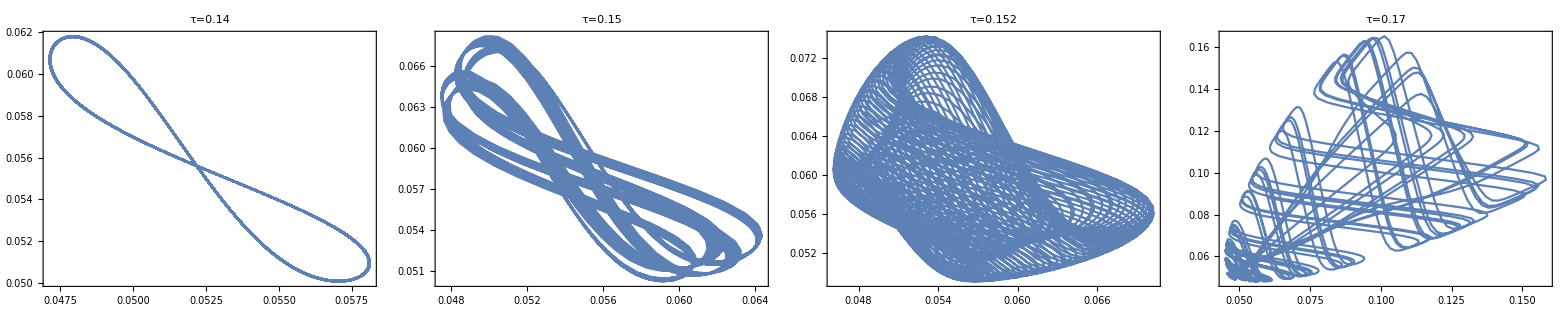

```mathematica
dh2=Grid[{{p2[0.14],p2[0.150],p2[0.152],p2[0.17]}}]
```